# 面向物理人的 Mathematica 简介

## 汇报人：尹琪钦 物理学21级 南京大学物理学院 211870080@smail.nju.edu.cn

## 软件安装

学校已购买正版软件，并在 ITSC 官网上给出了下载、激活链接和详细教学：
https://itsc.nju.edu.cn/Mathematica/list.htm
最新的 14.0 版本新增了若干 AI 相关的功能，值得体验！

## 软件简介

Wolfram  Mathematica  （简称：Mathematica） 是一款拥有强大的数值计算和符号运算能力的科学计算软件，广泛使用于科学、工程、数学、计算等领域，是目前为止使用最广泛的数学软件之一。其编程语言为Wolfram 语言，十分接近自然语言，甚至支持识别简单的自然语言输入，如：⟶。

Mathematica 的发布标志着现代科技计算的开始。自从 1988 年发布以来，它已经对如何在科技和其他领域运用计算机产生了深刻的影响。Mathematica 是世界上通用计算系统中最强大的系统之一。它与 MATLAB 和 Maple 并称为三大数学软件。

Mathematica 分为两部分：内核和前端。内核解释表达式并返回结果，而前端提供 GUI，允许用户创建和编辑“笔记本文档”，其中包含程序代码、公式、图像等。

在此简要介绍几条功能和特点：

符号-数值混合型方法：Mathematica 完美集成了符号和数值计算，使用户能够采用混合方法处理问题，确保在混合任意精度的条件下给出一致的结果。值得注意的是，给出的是物理系同学很爱的解析表达式！

```mathematica
Integrate[Exp[-α x^2],{x,-Infinity,Infinity}]
```

ConditionalExpression[(√π)/(√α), Re[α]>0]

图形绘制：使用一行代码即可绘制各种图形，包括二维和三维数据的可视化。

```mathematica
BubbleChart3D[RandomReal[1,{5,10,4}],ChartLegends->{"组1","组2","组3","组4","组5"}]
```

-Graphics3D-

良好的交互性：方便用户分段写代码、调试、注释几乎同时进行，减少大量debug 的时间，且适合制作高质量的课程笔记。

复杂性和广泛性：Mathematica 的核心设计使其涉及的领域不断增长，提供不错的跨学科体验，从数学和科技计算到许多其他计算领域，如金融、地球科学、数据科学…… 此外，对于物理而言，量子场论、广义相对论等技巧性强且繁琐的计算，Mathematica 也提供了相应的解决方案。

Mathematica 重点应用领域一览：
-Graphics-

强大全面的帮助文档、学习资源：

帮助文档：https://reference.wolfram.com/language/index.html.zh

“ListPlot3D”函数为例：
-Graphics-

面向数学学习的快速入门指南：https://www.wolfram.com/language/fast-introduction-for-math-students/zh/

Wolfram U Classes and Courses:  https://www.wolfram.com/wolfram-u/courses/catalog/

………… 更多等待你的探索

## 快速上手

### 1. 你可以将 Mathematica 看作某种高级的科学计算器

基础数学运算：代数、三角函数、数值……

```mathematica
1+1
```

2

```mathematica
Log[E^2]
```

2

```mathematica
Log[10,10^5]
```

5

```mathematica
Factor[(a+b+c)^5-a^5-b^5-c^5](*Factorization 轻松处理复杂因式分解*)
```

5 (a+b) (a+c) (b+c) (a^2+a b+b^2+a c+b c+c^2)

```mathematica
{Sin[60Degree],Sin[Pi/3]}(*三角函数运算，支持角度、弧度制*)
```

{(√3)/2,(√3)/2}

```mathematica
Exp[I Pi]
```

-1

```mathematica
E//N(*E 的数值*)
N[E,10](*数值运算，并指定精度*)
```

2.71828

2.718281828

不等式

x<1||2<x<3||x>4

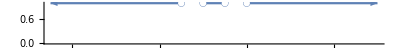

```mathematica
Reduce[(x-1) (x-2) (x-3) (x-4)>0,x](*求解不等式*)
NumberLinePlot[%,{x,-5,10}](*满足不等式区域的可视化*)
```

(x≤1/2 (1-√5)&&y<2-x^2)||(1/2 (1-√5)<x≤1/2 (1+√5)&&y<1-x)||(x>1/2 (1+√5)&&y<2-x^2)

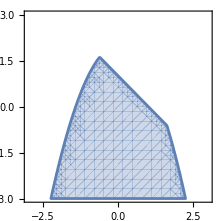

```mathematica
Reduce[{x^2+y<2&&x+y<1}]
RegionPlot[%,{x,-3,3},{y,-3,3}]
```

高等数学：极限、微分、积分、级数……

```mathematica
Limit[(Exp[(1+x)^(1/x)]-(1+x)^(E/x))/x^2,x->0](*一个比较复杂的求极限题目*)
TraditionalForm[HoldForm[Limit[(Exp[(1+x)^(1/x)]-(1+x)^(E/x))/x^2,x->0]]](*生成适合用作图片的表达式*)
TeXForm[%](*生成公式的LaTeX 表达式*)
```

ⅇ^(1+ⅇ)/8

(exp((1+x)^(1/x))-(1+x)^(ⅇ/x))/x^2x0

\underset{x\to 0}{\text{lim}}\frac{\exp \left((1+x)^{1/x}\right)-(1+x)^{e/x}}{x^2}

```mathematica
f[x_]:=Log[Log[Log[x]]];
f'[x]
D[Log[Log[Log[x]]],x]
```

1/(x Log[x] Log[Log[x]])

1/(x Log[x] Log[Log[x]])

```mathematica
Integrate[√((1-u)/u),u](*不定积分*)
Integrate[√((1-u)/u),{u,x,1},Assumptions->{0<x<1}](*带有参数 x 的定积分*)
```

√(-1+1/u) u-ArcTan[√(-1+1/u)]

-√((1-x) x)+ArcTan[√(-1+1/x)]

```mathematica
Series[Exp[x^2],{x,0,8}](*在 x=0 处，求表达式的Taylor 级数，近似到8阶*)
```

1+x^2+x^4/2+x^6/6+x^8/24+O[x]^9

向量与矩阵计算

（数据处理个人决定还是MATLAB矩阵处理更方便）
矩阵运算相关函数：
https://reference.wolfram.com/language/guide/MatrixOperations.html

数组元素提取

```mathematica
ary={{1,1,0},{2,0,1},{0,3,1},{5,7,7}};
ary[[1]](*First[ary]*)
ary[[1,1]]
ary[[;;,1]](*ary[[All,1]]*)
Dimensions[ary]
Flatten[ary]
```

{1,1,0}

1

{1,2,0,5}

{4,3}

{1,1,0,2,0,1,0,3,1,5,7,7}

```mathematica
(*两种点积记号*)
{a,b,c}.{x,y,z}
Dot[{a,b,c},{x,y,z}]
```

a x+b y+c z

a x+b y+c z

```mathematica
u={1,1,1};
v={2,0,0};
u.v
Cross[u,v]
ArcSin[Norm[Cross[u,v]]/(Norm[u]Norm[v])]
VectorAngle[u,v]
```

2

{0,2,-2}

ArcSin[√(2/3)]

ArcCos[1/(√3)]

```mathematica
m={{1,2,3},{4,5,6},{7,8,9}};
Det[m]
{TensorRank[m],MatrixRank[m]}
RowReduce[m]//MatrixForm
Inverse[m]
```

0

{2,2}

(1 | 0 | -1
0 | 1 | 2
0 | 0 | 0)

Inverse::sing: 矩阵 {{1,2,3},{4,5,6},{7,8,9}} 是奇异的.

Inverse[{{1,2,3},{4,5,6},{7,8,9}}]

```mathematica
Eigensystem[m]
m.{1,-2,1}
Tr[m]
```

{{3/2 (5+√33),-3/2 (-5+√33),0},{{-(-15-√33)/(33+7 √33),(4 (6+√33))/(33+7 √33),1},{-(15-√33)/(-33+7 √33),(4 (-6+√33))/(-33+7 √33),1},{1,-2,1}}}

{0,0,0}

15

```mathematica
CharacteristicPolynomial[m,x]
Factor[%,Extension->{√33}]
```

18 x+15 x^2-x^3

1/4 (15+3 √33-2 x) x (-15+3 √33+2 x)

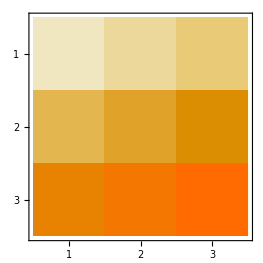

```mathematica
MatrixPlot[m](*矩阵可视化*)
```

张量积

```mathematica
s1={1,0};
s2={0,1};
σz={{1,0},{0,-1}};
KroneckerProduct[s1,s2]//Flatten//MatrixForm
KroneckerProduct[σz,σz]//MatrixForm
```

(0
1
0
0)

(1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | 1)

```mathematica
({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 1}}).({{0}, {1}, {0}, {0}})//MatrixForm
```

(0
-1
0
0)

以上的计算对应量子力学中：

```mathematica
Eigensystem[({{1, 0, 0, 0}, {0, -1, 0, 0}, {0, 0, -1, 0}, {0, 0, 0, 1}})]
```

{{-1,-1,1,1},{{0,0,1,0},{0,1,0,0},{0,0,0,1},{1,0,0,0}}}

带有量纲计算，并且自动实现单位转换

```mathematica
r=2 Quantity[, "Femtometers"]
ϵC=1/(4Pi Quantity[, "ElectricConstant"])Quantity[, "ElementaryCharge"]^2/r(*距离 2 fm 两个质子的Coulomb 力*)
UnitConvert[ϵC,Quantity[, "Megaelectronvolts"]]
QuantityMagnitude[%]
ϵG=-(Quantity[, "GravitationalConstant"] Quantity[, "ProtonMass"]^2)/r(*距离 2 fm 两个质子的引力*)
UnitConvert[ϵG,Quantity[, "Megaelectronvolts"]]
QuantityMagnitude[%]
```

2 fm

1/(8 π) e^2/(fm ε_0)

0.719982274 MeV

0.719982274

-1/2 m_p^2 G/fm

-5.827×10^-37 MeV

-5.827×10^-37

Manipulate 良好的交互体验！

调和数列求和

```mathematica
TraditionalForm[HoldForm[Sum[i^k,{i,1,n}]]]
Manipulate[Sum[i^k,{i,1,n}],{k,1,100,1}]
```

∑_(i=1)^n i^k

受迫振动随着参数的变化
-Graphics-
-Graphics-
研究  曲线随着阻尼项 , 本征频率  的变化
取

```mathematica
X[ω_]:=1/(√((2ω Subscript[ω, 0] ζ)^2+(Subscript[ω, 0]^2-ω^2)^2));
Manipulate[Plot[1/(√((2ω Subscript[ω, 0] ζ)^2+(Subscript[ω, 0]^2-ω^2)^2)),{ω,0,30},AxesLabel->{"ω","振幅"},PlotRange->{0,0.06}],{Subscript[ω, 0] ,0,30},{ζ,0,1}]
```

一定程度上减少繁琐且无意义计算所浪费的时间

### 2. 获得一些超出草稿纸的物理直觉

Mathematica 轻松的可视化功能帮助直观理解物理过程，建立物理直觉

矢量场可视化

```mathematica
A={y/(x^2+y^2+z^2), -x/(x^2+y^2+z^2), z/(x^2+y^2+z^2)};
SliceVectorPlot3D[A, "CenterPlanes", {x, -2, 2}, {y, -2,  2}, {z, -2, 2},PlotLegends->Automatic]
```

-Graphics3D-

-(2 z^2)/((x^2+y^2+z^2)^2)+1/(x^2+y^2+z^2)

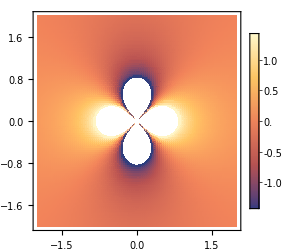

-Graphics3D-

```mathematica
Div[A,{x,y,z}]
(*由于散度有关于 z 轴的旋转对称性，绘制散度在 y=0 平面的密度图*)
DensityPlot[-(2 z^2)/((x^2+z^2)^2)+1/(x^2+z^2),{x,-2,2},{z,-2,2},PlotLegends->Automatic,PlotPoints->100]
(*还可以绘制矢量场旋度的可视化*)
SliceVectorPlot3D[Curl[A,{x,y,z}], "CenterPlanes", {x, -2, 2}, {y, -2,  2}, {z, -2, 2},PlotLegends->Automatic]
```

特殊函数可视化

Bessel 函数

(√(2/π) Cos[π/4-x])/(√x)

((-1)^(3/4) ⅇ^(-ⅈ x))/(√(2 π) √x)-((-1)^(1/4) ⅇ^(ⅈ x))/(√(2 π) √x)

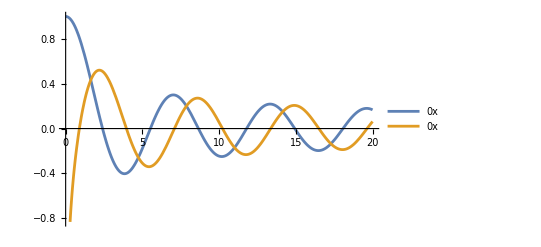

```mathematica
Series[BesselJ[0,x],{x,Infinity,0}]//Normal
Series[BesselY[0,x],{x,Infinity,0}]//Normal

Plot[{BesselJ[0,x],BesselY[0,x]},{x,0,20},PlotLegends->"Expressions"]
```

(ⅈ ⅇ^-x)/(√(2 π) √x)+ⅇ^x/(√(2 π) √x)

(ⅇ^-x √(π/2))/(√x)

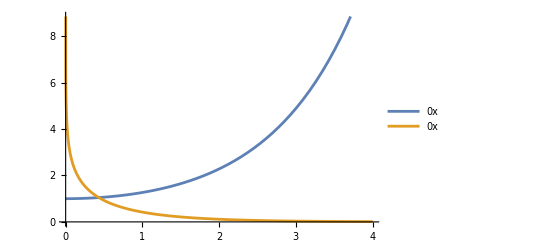

```mathematica
Series[BesselI[0,x],{x,Infinity,0}]//Normal
Series[BesselK[0,x],{x,Infinity,0}]//Normal

Plot[{BesselI[0,x],BesselK[0,x]},{x,0,4},PlotLegends->"Expressions"]
```

球谐函数：正交归一性、可视化

```mathematica
SphericalHarmonicY[3,1,θ,ϕ]
```

-1/8 ⅇ^(ⅈ ϕ) √(21/π) (-1+5 Cos[θ]^2) Sin[θ]

```mathematica
TraditionalForm[HoldForm[Integrate[SphericalHarmonicY[1,1,θ,ϕ]Conjugate[SphericalHarmonicY[1,1,θ,ϕ]]Sin[θ],{θ,0,Pi},{ϕ,0,2Pi}]]]
Integrate[SphericalHarmonicY[1,1,θ,ϕ]Conjugate[SphericalHarmonicY[1,1,θ,ϕ]]Sin[θ],{θ,0,Pi},{ϕ,0,2Pi}]
```

∫_0^π ∫_0^(2 π) Y_1^1(θ,ϕ) Conjugate[Y_1^1(θ,ϕ)] sin(θ)ⅆϕⅆθ

1

```mathematica
TraditionalForm[HoldForm[Integrate[SphericalHarmonicY[1,1,θ,ϕ]Conjugate[SphericalHarmonicY[1,0,θ,ϕ]]Sin[θ],{θ,0,Pi},{ϕ,0,2Pi}]]]
Integrate[SphericalHarmonicY[1,1,θ,ϕ]Conjugate[SphericalHarmonicY[1,0,θ,ϕ]]Sin[θ],{θ,0,Pi},{ϕ,0,2Pi}]
```

∫_0^π ∫_0^(2 π) Y_1^1(θ,ϕ) Conjugate[Y_1^0(θ,ϕ)] sin(θ)ⅆϕⅆθ

0

```mathematica
Y2=TransformedField["Spherical"->"Cartesian",(Abs[SphericalHarmonicY[l,m,θ,ϕ]])^2,{r,θ,ϕ}->{x,y,z}];
SliceDensityPlot3D[Y2/.{l->2,m->0}//N,{x^2+y^2+z^2==4},{x,-2,2},{y,-2,2},{z,-2,2}]
SphericalPlot3D[(Abs[SphericalHarmonicY[l,m,θ,ϕ]])^2/.{l->2,m->0}//N,{θ,0,Pi},{ϕ,0,2 Pi}]
```

-Graphics3D-

-Graphics3D-

### 3. 顺手处理个实验数据

适用于少量轻便的实验数据处理（譬如大学物理实验、近代物理实验）

```mathematica
DA={{608,8.04778},{799,10.5515},{960,12.6137},{1329,17.47934},{619,8.1461},{713,9.3431}}
```

{{608,8.04778},{799,10.5515},{960,12.6137},{1329,17.4793},{619,8.1461},{713,9.3431}}

```mathematica
LDA=LinearModelFit[DA,x,x](*线性拟合*)
```

FittedModel[…]

0.999922

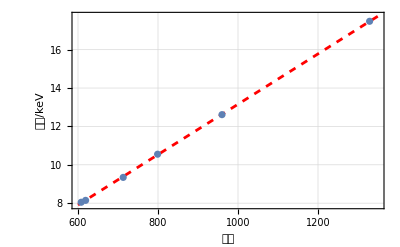

```mathematica
LDA["RSquared"]
Show[
Plot[LDA[x],{x,600,1350},PlotStyle->{Dashed,Red},PlotLegends->Placed[{"线性拟合"},{Left,Top}],GridLines->Automatic],
ListPlot[DA,PlotLegends->Placed[{"数据点"},{Left,Top}]],
Frame->True,FrameLabel->{"道址","能量/keV"}]
```

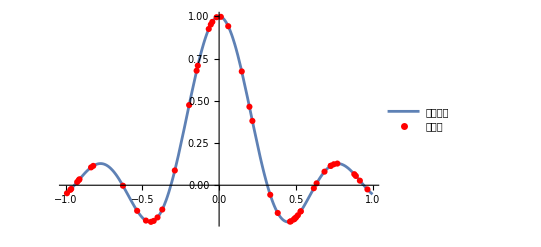

```mathematica
coord=RandomReal[{-1,1},50];
data=Transpose[{coord,Sinc[10 coord]}];(*通过随机数方法生成测试数据样本*)
degree=47;
basis=Table[ChebyshevT[k,x],{k,0,degree}];(*选择特殊的用于拟合的基底，拟合函数将是这些基底的线性组合*)
fit=Fit[data,basis,x];(*选择特定形式函数进行拟合*)
Show[Plot[fit,{x,-1,1},PlotLegends->{"拟合曲线"}],
ListPlot[data,PlotStyle->Red,PlotLegends->{"数据点"}]
]
```

在数据点所在范围内，拟合精度还是不错的

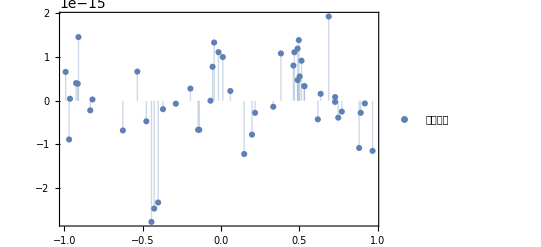

```mathematica
Δ=data;
Δ[[;;,2]]-=fit/.{x->data[[;;,1]]};
ListPlot[Δ,Frame->True,Filling->Axis,PlotLegends->{"拟合残差"}]
```